```mathematica
μ=4.38
ρ=51.0
L=150
Dia=2.900/12
Subscript[P, n]=15
Δz = 200
R= 22471*u
ϵ=0.00015
f=(-1.737*Log[(0.269*ϵ/Dia)-(2.185/R*Log[(0.269*ϵ/Dia)+14.5/R])])^-2
ℱ =Simplify[2*f*u^2*80/Dia ]
Manipulate[List[0.3314365221172562/Log[0.00016696551724137932-(0.00009723643807574207 Log[0.00016696551724137932+0.0006452761336834141/u])/u]^2, (219.4338353328041 u^2)/Log[0.00016696551724137932-(0.00009723643807574207 Log[0.00016696551724137932+0.0006452761336834141/u])/u]^2, 763.287,22471*u],{u,0,17}]
```

4.38

51.

150

0.241667

15

200

22471 u

0.00015

0.331437/Log[0.000166966-(0.0000972364 Log[0.000166966+0.000645276/u])/u]^2

(219.434 u^2)/Log[0.000166966-(0.0000972364 Log[0.000166966+0.000645276/u])/u]^2

```mathematica
Simplify[DSolve[{y''[x]+y[x]== Sin[x]}, y[x],x]]
```

{{y[x]→(-x/2+C[1]) Cos[x]+C[2] Sin[x]}}

48.013-2.33 x

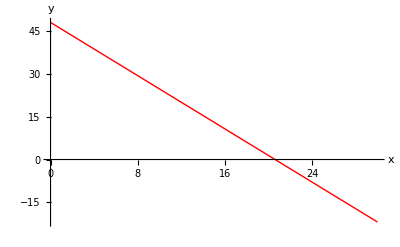

u

```mathematica
sol= 48.013-2.33*x
Plot[sol, {x, 0,30}, PlotStyle-> {Red, Thick}, AxesLabel->{x,y}, PlotLabels ->Placed[ "48.013-2.33x", Above]]
```

```mathematica
mat = {{25,206,8294},{206,2396,77177},{8294,77177,3531848}}.{Subscript[β, 0],Subscript[β, 1],Subscript[β, 2]}== {{725.82},{8008.47},{274816.71}}
{{25,206,8294},{206,2396,77177},{8294,77177,3531848}}//MatrixForm
Solve[mat]
```

{25 β_0+206 β_1+8294 β_2,206 β_0+2396 β_1+77177 β_2,8294 β_0+77177 β_1+3531848 β_2}=={{725.82},{8008.47},{274817.}}

(25 | 206 | 8294
206 | 2396 | 77177
8294 | 77177 | 3531848)

{{β_0→2.26379,β_1→2.74427,β_2→0.0125278}}

```mathematica
R = 52686.9/dia
f=(-1.737*Log[(0.269*ϵ/dia)-(2.185/R*Log[(0.269*ϵ/dia)+14.5/R])])^-2
fanning = 2.693*dia^5

Manipulate[List[0.3314365221172562/Log[0.00004035/dia-0.000041471409401578 dia Log[0.00004035/dia+0.0002752107260058952 dia]]^2,2.693 dia^5,52686.9/dia,(-1.737*Log[(0.269*ϵ/dia)-(2.185/(52686.9/dia)*Log[(0.269*ϵ/dia)+14.5/(52686.9/dia)])])^-2],{dia, 0, 1}]
```

52686.9/dia

0.331437/Log[0.00004035/dia-0.0000414714 dia Log[0.00004035/dia+0.000275211 dia]]^2

2.693 dia^5

```mathematica
mat2={{10,223,553},{223,5200.9,12352},{553,12352,31729}}
mat3={{Subscript[β, 0]},{Subscript[β, 1]},{Subscript[β, 2]}}
mat4 ={{1916},{43550.8},{104736.8}}

Solve[mat2.mat3== mat4]
```

{{10,223,553},{223,5200.9,12352},{553,12352,31729}}

{{β_0},{β_1},{β_2}}

{{1916},{43550.8},{104737.}}

{{β_0→171.055,β_1→3.71329,β_2→-1.12589}}

```mathematica
u
```

u

```mathematica
Dia = 2.9/12
```

0.241667

```mathematica
Dia = 2.9/12
u=(4*Q)/(Pi*Dia)
R= 22471*u

f=(-1.737*Log[(0.269*0.00015/Dia)-(2.185/R*Log[(0.269*0.00015/Dia)+14.5/R])])^-2
ΔP = -662.07*((4*Q)/(Pi*(2.9/12)))^2*0.3314365221172562/Log[0.00016696551724137932-(0.000018455918970999404 Log[0.00016696551724137932+0.00012247635015079695/Q])/Q]^2
P= D[ΔP, Q]

Plot[{ΔP, P}, {Q,0,3}, PlotLabels-> Automatic]
```

0.241667

5.26858 Q

118390. Q

0.331437/Log[0.000166966-(0.0000184559 Log[0.000166966+0.000122476/Q])/Q]^2

-(6091.03 Q^2)/Log[0.000166966-(0.0000184559 Log[0.000166966+0.000122476/Q])/Q]^2

(12182.1 Q^2 ((2.26041×10^-9)/((0.000166966+0.000122476/Q) Q^3)+(0.0000184559 Log[0.000166966+0.000122476/Q])/Q^2))/((0.000166966-(0.0000184559 Log[0.000166966+0.000122476/Q])/Q) Log[0.000166966-(0.0000184559 Log[0.000166966+0.000122476/Q])/Q]^3)-(12182.1 Q)/Log[0.000166966-(0.0000184559 Log[0.000166966+0.000122476/Q])/Q]^2

-Graphics-

```mathematica
Clear[R]
R = 35036.56
ϵ = 0.00015
Dia = 1.939/12
(-1.737*Log[(0.269*(ϵ/Dia))-((2.185/R)*Log[(0.269*(ϵ/Dia))+14.5/R])])^-2
```

35036.6

0.00015

0.161583

0.00629553